```mathematica
f=Import["/Users/tao/Learning/USTC/Physics/Hefei Large Cannon/sim.csv"]
```

{{x,y,z,vx,vy,vz,ax,ay,az,time},{5.58675,0.916653,13.8863,558.674,91.6653,1388.63,-4.94462,-0.348357,-40.3998,0.01},25366,{133862.,20075.8,-7.91688,499.818,79.7888,-1388.87,-3.95502,0.032467,-40.3591,253.68}}
 |  |  |  |

```mathematica
tf=Transpose[f]
```

{1}
 |  |  |  |

```mathematica
lxt=tf[[1]][[2;;]];
tt=tf[[10]][[2;;]];
xt=Transpose[{tt,lxt}];
lyt=tf[[2]][[2;;]];
yt=Transpose[{tt,lyt}];
lzt=tf[[3]][[2;;]];
zt=Transpose[{tt,lzt}];
lvxt=tf[[4]][[2;;]];
vxt=Transpose[{tt,lvxt}];
lvyt=tf[[5]][[2;;]];
vyt=Transpose[{tt,lvyt}];
lvzt=tf[[6]][[2;;]];
vzt=Transpose[{tt,lvzt}];
laxt=tf[[7]][[2;;]];
axt=Transpose[{tt,laxt}];
layt=tf[[8]][[2;;]];
ayt=Transpose[{tt,layt}];
lazt=tf[[9]][[2;;]];
azt=Transpose[{tt,lazt}];
```

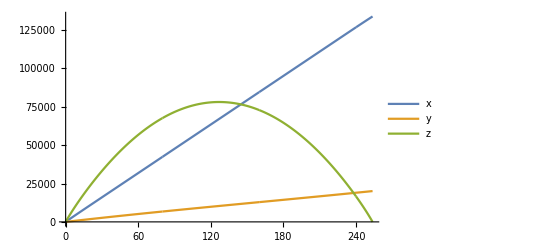

```mathematica
ListLinePlot[{xt,yt,zt},PlotLegends->{"x","y","z"}]
```

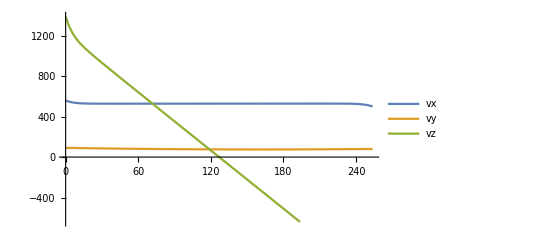

```mathematica
ListLinePlot[{vxt,vyt,vzt},PlotLegends->{"vx","vy","vz"}]
```

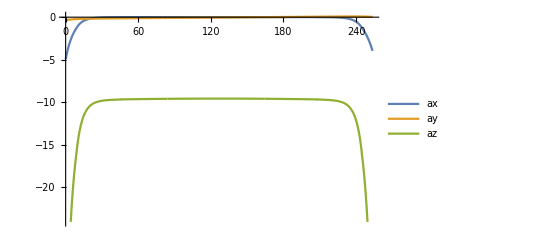

```mathematica
ListLinePlot[{axt,ayt,azt},PlotLegends->{"ax","ay","az"}]
```